# Bezier Curve

```mathematica
cp = {{0, 20}, {10, 40}, {20, 0}, {30, 20}};
```

## Bernstein Basis

```mathematica
Bernstein[n_, i_, t_] := n! / i! / (n-i)! (1-t)^(n-i)t^i
```

```mathematica
Bernstein[4, 2, 0.5]
```

0.375

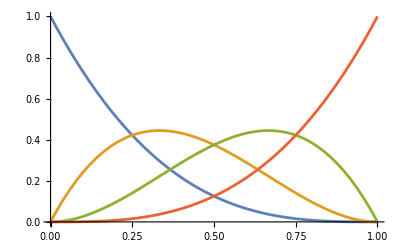

```mathematica
Plot[Evaluate[Table[Bernstein[Length[cp] - 1, i, t], {i, 0, Length[cp] -  1}]], {t, 0, 1}]
```

## Linear combination of Bernstein basis and control points

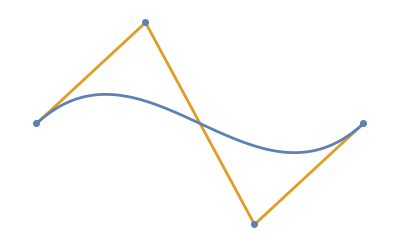

```mathematica
Show[
	ListPlot[{cp, cp}, Joined->{False, True}],
	ParametricPlot[
		Sum[
			cp[[i + 1]] * Bernstein[Length[cp] - 1, i, t]
			,{i, 0, Length[cp] - 1}
		]
		,{t, 0, 1}
	],
	PlotRange->All,
	Axes->False
]
```

## Monomial Matrix of Bezier curve

```mathematica
monomialMatrix = Table[Reverse[PadRight[CoefficientList[Bernstein[Length[cp] - 1, x, t], t], Length[cp], 0]], {x, 0, Length[cp] - 1}];
monomialMatrix // MatrixForm
```

(-1 | 3 | -3 | 1
3 | -6 | 3 | 0
-3 | 3 | 0 | 0
1 | 0 | 0 | 0)

## Implementation of Bezier curve using DeCasteljau Algorithm

```mathematica
DeCasteljau[cp_, t_] := Module[{points = cp, n = Length[cp], i, j},
	For[i = 1, i < n, i++, 
		For[j = 1, j <= n - i, j++, 
			points[[j]] = (1 - t) points[[j]] + t points[[j + 1]];
		]
	];
	points[[1]]
]
```

```mathematica
DeCasteljau[cp, t]
```

{(1-t) (10 (1-t) t+t (10 (1-t)+20 t))+t ((1-t) (10 (1-t)+20 t)+t (20 (1-t)+30 t)),t (40 (1-t)^2+20 t^2)+(1-t) (40 (1-t) t+(1-t) (20 (1-t)+40 t))}

```mathematica
cpList = {
			{{161, 244}, {147.83, 256.811}, {141.058, 271.922}, {141, 290}},
			{{141, 290}, {146.024, 309.687}, {146.024, 309.687}, {150, 329}},
			{{150, 329}, {149.108, 329.942}, {148.216, 331.187}, {147, 331}},
			{{163, 307}, {166.627, 317.753}, {158.656, 328.461}, {147, 331}},
			{{163, 317}, {161.78, 343.934}, {193.385, 366.479}, {203, 387}},
			{{174, 253}, {158.461, 281.973}, {178.863, 313.231}, {203, 331}},
			{{244, 243}, {256.067, 254.265}, {264.774, 268.759}, {266, 286}},
			{{266, 286}, {264.682, 298.326}, {258.436, 314.45}, {256, 327}},
			{{256, 327}, {256.675, 328.85}, {257.838, 329.859}, {259, 331}},
			{{244, 307}, {241.698, 318.677}, {248.848, 326.535}, {260, 331}},
			{{244, 316}, {245.64, 343.407}, {213.858, 366.481}, {203, 387}},
			{{231, 253}, {249.172, 281.975}, {226.195, 313.054}, {203, 331}}
};
```

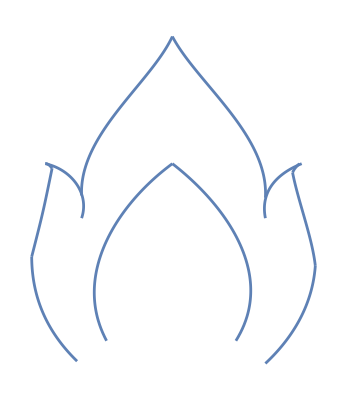

```mathematica
Show[
	Table[
		ParametricPlot[DeCasteljau[cpList[[i]], t], {t, 0, 1}]
		,{i, 1, Length[cpList]}
	], PlotRange->All, Axes->False
]
```